```mathematica
$Machine
```

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$DefaultRemoteKernel="ssh://phy2";
```

```mathematica
$DefaultRemoteKernel="localhost"
```

localhost

```mathematica
Get["Gdef.wl"]
```

```mathematica
G[1,2,3,4]
```

{{0.000042788,9.44999×10^-6},{9.44999×10^-6,0.0000309426}}

```mathematica
packageCode=Import["BiharmonicSolverFourier.wl","Text"];
```

```mathematica
RemoteEvaluate[$ProcessorCount]
```

48

```mathematica
values=RemoteEvaluate[
LaunchKernels[2$ProcessorCount];
cfG=Compile[{x1,y1,x2,y2},G[x1,y1,x2,y2]//Evaluate];
ToExpression[packageCode];
sol=BiharmonicSolver`solveBiharmonicFourier[cfG,128,8.0,"Method"->"Compiled"];
values=Flatten[Table[{sol["grid"][[i]],sol["grid"][[j]],sol["f"][[i,j,i,j]]},{i,sol["n"]},{j,sol["n"]}],1];
values
];
```

===============================================

Biharmonic Fourier Solver

===============================================

Grid size: 32^4 = 1048576 points

Domain: [-8., 8.]^2 x [-8., 8.]^2

Method: Compiled

-----------------------------------------------

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (17.12 s)

Memory for G components: ~32. MB

[Step 2/4] Computing 4D FFT of G components...

Done. (0.14 s)

[Step 3/4] Pointwise division in Fourier space...

-8
  Regularization eps = 2.27 Ã.97 10

Done. (0.36 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (0.04 s)

-----------------------------------------------

Max |f| = 4.028

Solution complete.

===============================================

LinkObject::linkd: Unable to communicate with closed link LinkObject[ssh -4 -x -o StrictHostKeyChecking=no -o BatchMode=yes phy2 wolfram -noinit -wstp,408,20].

KernelObject::badlink: RemoteEvaluate could not read from link LinkObject[ssh -4 -x -o StrictHostKeyChecking=no -o BatchMode=yes phy2 wolfram -noinit -wstp,408,20].

```mathematica
RemoteEvaluate[Length@LaunchKernels[4]]
```

4

```mathematica
ParallelEvaluate[Length@LaunchKernels[], remote]
```

LaunchKernels::subnopar: Parallel programming is not available in subkernels of another parallel computation.

0

ssh://phy2

```mathematica
$DefaultRemoteKernel=KernelConfiguration["ssh://phy2"]
```

KernelConfiguration[…]

```mathematica
$MachineName
```

Mac

```mathematica
RemoteEvaluate[$MachineName]
```

compute2

```mathematica
RemoteEvaluate[$ProcessID]
```

1001127

```mathematica
RemoteEvaluate[$ProcessID]
```

1001565

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ashmat/Desktop/fluctuation-solver

```mathematica
remote=SubprocessKernelOpen[<|"Host"->"phy2","RemoteCommand"->"/usr/local/bin/WolframKernel"|>]
```

SubprocessKernelOpen[<|Host→phy2,RemoteCommand→/usr/local/bin/WolframKernel|>]

```mathematica
Quit
```

```mathematica
params={S0->1,l->1};
W=10;
S[r_]:=S0 f[r/l]
f[x_]:=x √((0.34+0.07 x^2)/(1+0.41 x^2+0.07 x^4))
θ[ϕ_]:=ϕ/2
Q[x_,y_]:={{S[r] Cos[2θ[ϕ]],S[r] Sin[2θ[ϕ]]},{S[r] Sin[2θ[ϕ]],-S[r] Cos[2θ[ϕ]]}}/.{r->√(x^2+y^2),ϕ->ArcTan[x,y]}
```

```mathematica
A[x_,y_]:=3IdentityMatrix[2]+Q[x,y]
Λ[x_,y_]:=3IdentityMatrix[2]+0Q[x,y]
G[x1_,y1_,x2_,y2_]=(A[x1,y1]Exp[-{x1-x2,y1-y2}.Λ[x1,y1].{x1-x2,y1-y2}/2]
+A[x2,y2]Exp[-{x1-x2,y1-y2}.Λ[x2,y2].{x1-x2,y1-y2}/2])/.params//Simplify;
```

```mathematica
cfG=Compile[{x1,y1,x2,y2},G[x1,y1,x2,y2]//Evaluate];
```

```mathematica
(*Run solver*)
```

```mathematica
LaunchKernels[];(*start parallel kernels if not already running*)
```

```mathematica
sol=solveBiharmonicFourier[cfG,80,8.0,"Method"->"Compiled"];
```

═══════════════════════════════════════════════

Biharmonic Fourier Solver

═══════════════════════════════════════════════

Grid size: 80^4 = 40960000 points

Domain: [-8., 8.]^2 x [-8., 8.]^2

Method: Compiled

───────────────────────────────────────────────

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (4.74 s)

Memory for G components: ~1250. MB

[Step 2/4] Computing 4D FFT of G components...

Done. (1.8 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 5.81×10^-10

Done. (4.06 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (0.26 s)

───────────────────────────────────────────────

Max |f| = 4.027

Solution complete.

═══════════════════════════════════════════════

```mathematica
values=Flatten[Table[{sol["grid"][[i]],sol["grid"][[j]],sol["f"][[i,j,i,j]]},{i,sol["n"]},{j,sol["n"]}],1];
```

```mathematica
ListPlot3D[values,PlotRange->All,PlotLabel->"f(r, r)"]
```

-Graphics3D-

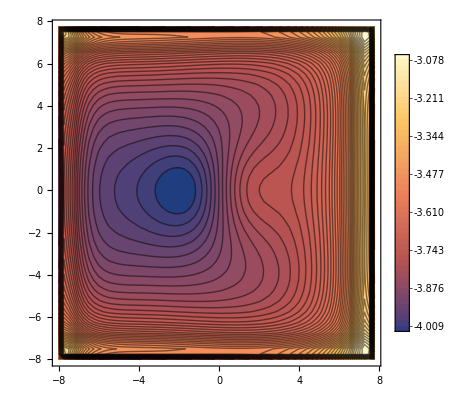

```mathematica
ListContourPlot[values, Contours->50,PlotLegends->Automatic]
```

```mathematica
(*Visualize diagonal slice f(x,y,x,y)*)
fDiag=Table[sol["f"][[i,j,i,j]],{i,sol["n"]},{j,sol["n"]}];
ListPlot3D[fDiag,PlotRange->All,PlotLabel->"f(r, r)"]
(*Visualize f(x,y,0,0)*) 
slice=extractSlice[sol,0.,0.];
ListPlot3D[slice["slice"],DataRange->{{-8,8},{-8,8}},PlotRange->All,PlotLabel->"f(r, 0)"]
(*Build interpolating function for arbitrary evaluation*) fInterp=buildInterpolation[sol];
fInterp[1.0,0.5,-0.3,0.2]  (*evaluate at any point*)
```

-Graphics3D-

-Graphics3D-

-2.27125